# Efficient Bayesian Regression by Kalman Folding

Brian Beckman
4 Mar 2018

## Abstract

Linear systems appear everywhere, and, where they don’t appear naturally, linear approximations abound because non-linear systems are often intractable. Examples comprise machine learning, control, dynamics, robotics, and many more. 

Linear regression is the standard technique for estimating the coefficients or parameters of a linear model for given data. Often, authors sweep linear regression under the rug, presumably because readers know all about it. However, time and again, I see the normal equations directly applied (fat, slow, over-fitting), .7fmatrices inverted (risky), and neural networks applied (overkill).

Over-fitting means that linear models, as their order (number of parameters) nears or exceeds the number of data points, tend to follow noisy data too well, limiting their smoothness and predictive power outside the bounds of the data. Models that over-fit “wiggle” too much and generalize poorly.

Regularization is the usual technique for controlling over-fitting. In Bayesian approaches, regularization is introduced by providing a-prior belief hyperparameters. We show here, numerically, that these Bayesian hyperparameters are the a-priori observation noise covariance and the a-priori estimate covariance of Kalman filtering. These covariances are concrete and can be estimated or learned directly from experimental conditions. They are less abstract and easier to intuit than Bayesian hyperparameters.

Kalman filtering proffers scaling advantages over typical presentations of regularized Bayesian regression. These presentations are modifications of the normal equations from maximum-likelihood (MLE) regression. The normal equations and their Bayesian counterparts, the Maximum A-Posteriori or MAP equations, compute explicitly over whole data sets, limiting scalability. Kalman filtering is recurrent, meaning that it processes data one observation at a time, avoiding storage, multiplication, and inversion of large matrices of data. Kalman filtering has natural expression as a functional fold, fitting well with contemporary programming languages.

## Motivating Example

First, we exhibit recurrent least-squares (RLS), Kalman folding (KAL), and maximum-likelihood estimation (MLE) for a problem of order two: estimating the slope and intercept of a best-fit line to noisy data. The purpose of this example is to put an elementary problem into a setting that we generalize to higher order below. We do not explore over-fitting in this example, leaving that to the later one. 

MLE is computed using (1) Wolfram built-in functions, (2) directly through the classic normal equations, (3) using the Moore-Penrose left pseudoinverse, and (4) by sidestepping the risky inverse by solving a linear system. These methods of MLE yield exactly the same results for this small example. It is easy to make them diverge numerically for models with more parameters, that is, of larger order.

PROBLEM STATEMENT: Find best-fit, unknowns m (slope) and b (intercept), where z=m x+b, given known, noisy data (z_1,z_2,…,z_k) and (x_1,x_2,…,x_k). 

Write this system as a matrix equation and remember the symbols Ζ (observations, known), A (partials, known), and Ξ (model, state, unknown parameters to be estimated). Rows of Ζ and A come in matched pairs.

Ζ_(k×1)  =  (z_1
z_2
⋮
z_k)   =   (x_1 | 1
x_2 | 1
⋮ | ⋮
x_k | 1)  ·  (m
b)   +  noise   
=  A_(k×2)·Ξ_(2×1)  +  samples of NormalDistribution[0,σ_Ζ]

Ground Truth

Fake some data by (1) sampling a line specified by ground truth m and b, then (2) adding Gaussian noise. Run the faked data through various estimation procedures and see how close the estimated m and b come to the ground truth. In real-world applications, we rarely have ground truth. Its purpose is to baseline or calibrate the various methods.

```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

Partials

The partials A are a (column) vector of covectors (row vectors). Each covector is the gradient 1-form of A·Ξ with respect to Ξ, evaluated at specific values of Ξ from the data. Gradients are best viewed as 1-forms, always covectors, linear transformations of vectors.

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
Short[partials,3]
```

{{-1.,1.},{-0.966102,1.},{-0.932203,1.},{-0.898305,1.},«111»,{2.89831,1.},{2.9322,1.},{2.9661,1.},{3.,1.}}

Faked Observations Ζ

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[
RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},
{i,n}];
```

```mathematica
ClearAll[data,noiseSigma];
noiseSigma=0.65;
data=fake[nData,noiseSigma,partials,groundTruth];
Short[data,3]
```

{-0.573906,-0.979942,-0.96237,0.0088175,«111»,-0.24636,0.50719,1.21321,1.85373}

Wolfram Built-In

The Wolfram built-in LinearModelFit computes an MLE for Ξ=(m
b). The estimated m and b are reasonably close to the ground truth.

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,x,x];
Normal[model]
```

-0.399017+0.473514 x

Un-comment the following line to see everything Wolfram has to say about this MLE (it’s a lot of data).

```mathematica
(*Association[(#->model[#])&/@model["Properties"]]*)
```

The plot shows that Wolfram does an acceptable job, for practical purposes, of estimating the parameters m and b that define the line. We have 119 data and two parameters to estimate, so over-fitting will not be an issue.

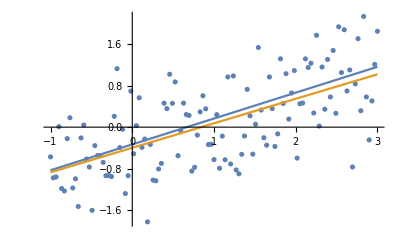

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m x+b,model[x]},{x,min,max}]]
```

Normal Equations

Solve equation 1 for a value of Ξ that minimizes sum-squared error J(Ξ)=^def(Ζ-A·Ξ)ᵀ·(Ζ-A·Ξ). That is the same as maximizing the likelihood of the data given the parameters, p ( Z|Ξ ). Because the noise 𝒩(0,σ) has zero mean, The solution turns out to be exactly what one would get from naive algebra:  Aᵀ·A is square. When it is invertible,

(Aᵀ·A)^-1·Aᵀ·Z  =  Ξ

That gives numerically the same answer as Wolfram’s built-in:

```mathematica
Inverse[partialsᵀ.partials].partialsᵀ.data
```

{0.473514,-0.399017}

### Moore-Penrose PseudoInverse

The matrix (Aᵀ·A)^-1·Aᵀ is the Moore-Penrose left pseudoinverse. Wolfram has a built-in for it. We get exactly the same answer as above:

```mathematica
PseudoInverse[partials].data
```

{0.473514,-0.399017}

### Avoiding Inversion

Avoid the inverse via LinearSolve. We have more to say about avoiding inverses below.

```mathematica
LinearSolve[partialsᵀ.partials,partialsᵀ].data
```

{0.473514,-0.399017}

### Don’t Use the Normal Equations

(Aᵀ·A)^-1·Aᵀ·Ζ is a nasty computation: in memory usage, in time, and in numerical risk. We see below that direct application of the maximum a-posteriori (MAP) equations suffer from the same hazards. How to avoid these hazards? Find a recurrence relation.

## Recurrence

Fold this recurrence over Ζ and A:

ξ←(Λ+aᵀ·a)^-1·(aᵀ·ζ+Λ·ξ)
Λ←(Λ+aᵀ·a)

where

ξ is the current estimate of Ξ

a and ζ are matched rows of A and Ζ

Λ accumulates Aᵀ·A.

### Derivation Sketch

Derive the recurrence as follows: Treat the estimate-so-far,

ξ_(so-far)=^def(Aᵀ·A)^-1·Aᵀ·Ζ_(so-far)

as just one more (a-priori) observation with information matrix (proportional to inverse covariance)

Λ=A_(so-far)ᵀ·A_(so-far)

The scalar performance or squared error of the estimate, so far, is

J(ξ)  =  (Ζ_(so-far)-A_(so-far)·ξ)ᵀ·(Ζ_(so-far)-A_(so-far)·ξ)  =  (ξ-ξ_(so-far))ᵀ·Λ·(ξ-ξ_(so-far))

where ξ is the unknown true parameter vector, Ζ_(so-far) is the column vector of all observations so-far, and Λ=A_(so-far)ᵀ·A_(so-far) . Adding a new observation, ζ and its corresponding partial row covector a, increases the error J(ξ) by (ζ-a·ξ)ᵀ·(ζ-a·ξ). Minimize the new total error with respect to ξ to find the recurrence (exercise). ■

### Numerical Demonstration

Bootstrap the recurrence with initial values of ξ and Λ, namely ξ_0 and Λ_0.

Start with ξ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)).

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{Inverse[Π].(aᵀ.ζ+ Λ.ξ),Π}];

MatrixForm/@
({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.473514
-0.399017),(280.356 | 119.
119. | 119.)}

The estimates mBar and bBar are, numerically, the same as we got from Wolfram’s built-in. For this example, the choice of ξ_0 and Λ_0 had negligible effect.

### Structural Notes

The mappings of List over the data and partials convert them into column vectors. Wolfram built-ins and the normal equations, implicitly, treat one-dimensional lists as columns or rows as needed, then compute inner (dot) products as if the distinction did not matter. Python’s numpy has the same dubious feature.

### Memory and Time Efficiency

The required memory for the recurrence is O(Μ), where Μ is the order of the model, the number of parameters to estimate, length of Ξ, the length of each row of A. There is no dependency at all on the number k of data items. Also, the recurrence accumulates data one observation at a time, and is thus O(k), where k is the number of data. Contrast with the normal equations, which multiply and invert matrices at much greater cost.

### Check the A-Priori

The final value of Λ (called Π in the code, a returned value), is A_full ᵀ·A_full+Λ_0. To check the code, check that the difference between Π and A_full ᵀ·A_full is Λ_0:

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0.},{0.,1.×10^-6}}

### Covariance of the Estimate

The covariance of this estimate Ξ is ((n-1)/(n-2))*Variance [ Ζ-A·Ξ ]*Λ^-1 except for a small contribution from the a-priori information Λ_0. The correction factor ((n-1)/(n-2)) is a generalization .7fof Bessel’s correction. The 2 in (n-2) in the denominator is the number of parameters being estimated (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). The denominator of the correction, in general, is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

(0.00274951 | -0.00274951
-0.00274951 | 0.00647765)

Except for the reversed order, this is the same covariance matrix that Wolfram’s LinearModel reports:

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

(0.00274951 | -0.00274951
-0.00274951 | 0.00647765)

Don’t Invert That Matrix.7f

See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/ 

In general, replace any occurrence of A^-1·B or Inverse[A].B with LinearSolve[A,B] for arbitrary square matrix A and arbitrary matrix B.

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ξ)],Π}];

MatrixForm/@({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.473514
-0.399017),(280.356 | 119.
119. | 119.)}

Because this example is small, Inverse has no obvious numerical issues. It is very easy to produce large, ill-conditioned matrices, and one will spend a lot of time and storage inverting them, only to get useless results.

Interim Conclusions

We have eliminated memory bloat by processing updates one observation at a time, each with its paired partial. We reduce computation time and numerical risk by solving a linear systems instead of inverting a matrix. We also avoid matrix multiplications, which are approximately O(k^3).

## Sidebar: Estimating 1-Forms (Gradients)

In linear algebra, vectors are conventionally columns, i.e., n×1 matrices, and covectors are rows, i.e., 1×n matrices (see Vector Calculus, Linear Algebra, and Differential Forms, A Unified Approach by John H. Hubbard and Barbara Burke Hubbard). In this language, dual means transpose.

When the model --- the thing we’re estimating --- is a covector (row-vector), e.g., a 1-form, we have the dual (transposed) problem to the one above. This situation arises in reinforcement learning by policy gradient, for example. In that case, the observations Ω and the model Γ are now.7f covectors with elements ω and γ  instead of ζ and ξ. The co-partials Θ (replacing A) are now a covector of column vectors θ. The observation equation looks like Ω=Γ·Θ and the error-so-far like (x-γ)·Λ·(x-γ)ᵀ, where Λ=Θ_(so-far)·Θ_(so-far)ᵀ. We don’t change the name of Λ because it’s symmetric. Adding a new observation ω introduces new error (ω-x·θ)·(ω-x·θ)ᵀ. Minimizing the total error yields

γ←(γ·Λ+ω·θ ᵀ ).(Λ+θ·θ ᵀ )^-1
Λ←(Λ+θ·θ ᵀ )

straight transposes of equation 3. LinearSolve operates on the transposed right-hand side of the recurrence, and we transpose the solution to get the recurrence. We apply this dual model to the transpose of the original data:

```mathematica
Short[Transpose/@List/@partials,3]
```

{{{-1.},{1.}},{{-0.966102},{1.}},{{-0.932203},{1.}},{{-0.898305},{1.}},«112»,{{2.9322},{1.}},{{2.9661},{1.}},{{3.},{1.}}}

```mathematica
ClearAll[coUpdate];
coUpdate[{γ_,Λ_},{ω_,θ_}]:=
With[{Π=(Λ+θ.θᵀ)},
{LinearSolve[Π,Λ.γᵀ+θ.ωᵀ]ᵀ,Π}];
MatrixForm/@Fold[coUpdate,
{({{0, 0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@List/@data,Transpose/@List/@partials}ᵀ]
```

{(0.473514 | -0.399017),(280.356 | 119.
119. | 119.)}

Application of the Dual Problem

The finite-difference method of policy-gradient machine learning provides an example of this dual problem (see http://www.scholarpedia.org/article/Policy_gradient_methods). 

Imagine a scalar function J(θ) of a column K-vector θ_(K×1). We want to estimate its gradient covector ∇J, given a batch of ℐ random increments ΔΘ_(K×ℐ), from the system ∇J·ΔΘ=Δ J. Here, ∇J takes the role of the model whose state parameters Γ we want to estimate, ΔΘ takes the role of the partials of the model w.r.t. those parameters, and Δ J takes the role of measured data. Let Δ J_(ℐ×1) be a batch of observed increments to J and ΔΘ_(K×ℐ) be a matrix of the ℐ corresponding column-vector random increments to the input vectors θ_(K×1). The right pseudoinverse RPI=^def(ΔΘ_(K×ℐ)·ΔΘ_(K×ℐ)^ᵀ)^-1·ΔΘ_(K×ℐ)^ᵀ solves ∇ J_(ℐ×1)·ΔΘ_(K×ℐ)=Δ J_(ℐ×1) to yield ∇ J_(ℐ×1)≈Δ J_(ℐ×1)·RPI. 

Instead of the pseudoinverse, which is large, slow, and risky, use the co-update recurrence for this problem.

## Regularization By A-Priori in RLS and KAL

Chris Bishop’s Pattern Recognition and Machine Learning has an extended example fitting higher-order polynomials, linear in coefficients, starting in section 1.1. The higher the order of the polynomial, the more MLE over-fits. Bishop presents maximum a-posteriori or MAP regularization as a cure for this over-fitting. RLS and KAL already regularize, by construction. In this section, we relate their regularizations to MAP’s.

RLS and KAL each require an a-priori estimate and an a-priori uncertainty to bootstrap recurrences. RLS takes the estimate of uncertainty as an information matrix. KAL takes the estimate of uncertainty as a covariance matrix. KAL additionally requires an estimate of observation noise, which arises in real problems and can often be estimated out-of-band. We shall see that RLS must be renormalized with observation noise.

Reproducing Bishop’s Example

### Bishop’s Training Set

First, a sequence of n inputs for a training set, equally spaced in [0..1]. Like MATLAB linspace.

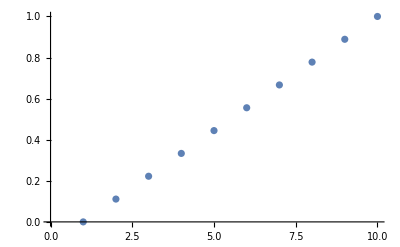

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[n_]:=Array[Identity,n,{0.,1.}];
ListPlot[bishopTrainingSetX[10]]
```

Bishop’s ground truth is a single cycle of a sine wave. Add noise to a sample taken at the values of the training set X. Bishop doesn’t state his observation noise, but I guess σ_z=σ_t=0.30 to create the fake data set.

Wolfram’s built-in NormalDistribution takes the standard deviation as its second argument, not the variance. Mixing up standard deviation and variance is an easy mistake. Bishop’s notation for normal distribution takes variance as second argument, so beware.

```mathematica
ClearAll[bishopTrainingSetY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopTrainingSetY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Take a sample and assign it the names bts for bishopTrainingSet. It isn’t his actual training set, which I didn’t find in print, just my simulation.

```mathematica
ClearAll[bishopTrainingSet,bts,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopTrainingSetY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bts=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

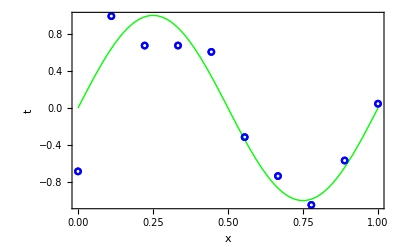

```mathematica
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

### Partials: Gradients of the Unknown Parameters

Write a function for partials. Quietly map the indeterminate 0^0 to 1. Test it symbolically.

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
MatrixForm@partialsFn[6,{Subscript[x, 1],Subscript[x, 2],Subscript[x, Μ]}]
```

(1 | x_1 | x_1^2 | x_1^3 | x_1^4 | x_1^5 | x_1^6
1 | x_2 | x_2^2 | x_2^3 | x_2^4 | x_2^5 | x_2^6
1 | x_Μ | x_Μ^2 | x_Μ^3 | x_Μ^4 | x_Μ^5 | x_Μ^6)

### The MAP Equations

Confer Bishop’s equation 3.3, page 138, where he writes the parameters to estimate as w and the observation equation as

y(x, w)=∑_(j=0)^Μ w_j ϕ_j (x)

(bias incorporated as coefficient of 0^th basis function). This is predictive: you give me concrete inputs x, parameters w, and I’ll give you a predicted observation y in terms of a number of basis functions ϕ equal in length to the number of parameters. For polynomial basis functions, the number of parameters is one more than the order Μ of the polynomials. 

Bishop (inexplicably) converts w into a covector and writes

y(x, w)=wᵀϕ (x)

where ϕ (x) is an (Μ+1)-dimensional column-vector of basis functions, the transpose of one row of our partials matrix A. I claim it’s better always to think of partials or gradients as values of differential forms, thus covectors (row vectors or covariant vectors, see https://goo.gl/DkeVmM, https://goo.gl/JgzqLR, and https://goo.gl/4TcF4T). 

To find best-fit values for w, rows of the partials matrix A are the covector gradients of y with respect to w. We prefer to write

observations as an Ν-dimensional column-vector Ζ_(Ν+1) with elements ζ_(j ∈ [ 1 ..Ν ])

the model (Μ+1)-dimensional column-vector as Ξ_((Μ+1)×1) with elements ξ_(i ∈ [ 1 ..Μ ])

partials matrix as A_(N×N)

Bishop calls our partials matrix the design matrix in his equation 3.16, page 142, consisting of values of the basis functions at the concrete inputs x_(n ∈ [1..N]). Bishop must (more cumbersomely) work in the dual of our formulation. 

We prefer to write as follows: the covector rows of the design matrix terms as polynomial basis functions evaluated at the input points x_(n ∈ [1..Ν]):

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (1 | x_1 | x_1^2 | ⋯ | x_1^M
1 | x_2 | x_2^2 | ⋯ | x_2^M
⋮ | ⋮ |   | ⋱ | ⋮
1 | x_N | x_N^2 | ⋯ | x_N^M)  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

then packed up into rows of the A matrix.

Z  =  A·Ξ  =  (ζ_0
ζ_1
⋮
ζ_Ν)  =   (A_(1×Μ)(x_1)
A_(1×Μ)(x_2)
⋮
A_(1×Μ)(x_Ν))_(Ν×Μ)  ·  (ξ_0
ξ_1
⋮
ξ_Μ)  +  noise

### MLE: The Normal Equations

Mechanize the normal equations for comparison purposes; we expect them to over-fit.

```mathematica
ClearAll[mleFit];
mleFit[Μ_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
PseudoInverse[partialsFn[Μ,xs]].ys];
mleFit[3,bts]
```

{-0.525434,13.62,-36.6964,23.7294}

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
```

The normal equations as a symbolic polynomial:

```mathematica
ClearAll[x];
Manipulate[
symbolicPowers[x,Μ].mleFit[Μ,bts],
{{Μ,3,"polynomial order Μ"},0,16,1,Appearance->{"Labeled"}}]
```

### RLS: Recurrent Least Squares

RLS is regularized by its a-priori estimate and a-priori information matrix. Use the slider below to see that once the minimum info becomes too large, the Λ matrix becomes ill-conditioned: pink warning message appear from the Wolfram kernel, and the solution is numerically suspect.

```mathematica
ClearAll[rlsFit];
rlsFit[σ2Λ_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,order+1],
Λ0=σ2Λ*IdentityMatrix[order+1]},
Fold[update,{ξ0,Λ0},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];

Manipulate[
rlsFit[10^-logσ2Λ][3,bts]⟦1⟧,
{{logσ2Λ,9.034},0,16,Appearance->"Labeled"}]
```

### KAL: Foldable Kalman Filter

The foldable Kalman filter (KAL) follows below. This version has only the update phase of a typical Kalman filter because the parameters are constant and there is no predict phase.

Note the Ζ parameter, the first in the definition of kalmanUpdate. This is the covariance matrix of the observation noise: it is not a column vector of all observations, it is not a standard deviation, and it is not the a-priori covariance P_0 of the parameter estimate. It is a constant throughout the folding run of the filter. That’s why it’s lambda-lifted into its own function slot; kalmanUpdate, called with some concrete value of Ζ, yields a function that can be folded over an a-priori estimate ξ_0 and covariance P_0 and a sequence of observation-partial-covector pairs {ζ,a}.

```mathematica
ClearAll[kalmanUpdate,kalFit];
kalmanUpdate[Ζ_][{ξ_,P_},{ζ_,a_}]:=
Module[{D,KT,K,L},
D=Ζ+a.P.aᵀ;
KT=LinearSolve[D,a.P];K=KTᵀ;
L=IdentityMatrix[Length[P]]-K.a;
{ξ+K.(ζ-a.ξ),L.P}];

kalFit[σζ2_,σξ2_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{ξ0=List/@ConstantArray[0,order+1],
P0=σξ2*IdentityMatrix[order+1]},
Fold[kalmanUpdate[σζ2*IdentityMatrix[1]],
{ξ0,P0},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];
```

### See All Three

The following interactive demonstration shows mleFit (normal equations), rlsFit (recurrent least squares), and kalFit (Kalman folding) on Bishop’s training set.

When the a-priori information matrix in RLS is 10^-6, and when the a-priori covariance of the a-priori estimate in KAL is 10^6, both produce regularized fits. In contrast, the MLE over-fits a 9^th-order polynomial by interpolating (going through) every data point because a 9^th-order polynomial fits ten data points exactly: the normal equations are neither overdetermined nor underdetermined at order nine, but accidentally constitute an exactly solvable linear system.

Increasing logΛ decreases the a-priori information matrix in RLS. Increasing logσξ2 increases the a-priori covariance of the estimate in KAL. Eventually. They eventually both over-fit the data completely and align with MLE. Run the polynomial order up to nine, then logΛ and logσξ2 all the way to the right, to their maximum values.

```mathematica
Manipulate[
Module[{x},(* gensym: fresh variable name *)
With[{
terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{
recurrent=Quiet@rlsFit[10^-logΛ0][Μ,bts],
normal=mleFit[Μ,bts],
kalman=kalFit[bishopFakeSigma^2,10^logσξ2][Μ,bts]},
With[{
rlsFn={terms}.recurrent⟦1⟧,
mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{
{Grid[{{
Button["RESET",(Μ=9;logΛ0=3;logσξ2=3)&],
Control[{{rlsQ,True,"RLS"},{True,False}}],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mleQ,True,"MLE"},{True,False}}]}}]},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logΛ0,3,"-log a-priori info (RLS)"},0,16,Appearance->"Labeled"}]},{Control[{{logσξ2,3,"log a-priori cov (KAL)"},0,16,Appearance->"Labeled"}]}}]]
```

Renormalizing RLS to KAL

When the observation noise Ζ is unity, KAL coincides with RLS. Below, we set a-priori information Λ in RLS to be always the inverse of a-priori estimate covariance P in KAL. Vary the observation noise independently to see KAL and RLS coincide.

As observation noise decreases, the solutions “trust” observations more and the solution over-fits. As the a-priori covariance decreases, the solution trusts a-priori estimates more and the solution regularizes.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧},
With[{recurrent=Quiet@rlsFit[10^(-2logσξ)][Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{rlsFn={terms}.recurrent⟦1⟧,
kalFn={terms}.kalman⟦1⟧},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[rlsQ,AppendTo[showlist,Plot[rlsFn,{x,0,1},PlotStyle->{Purple}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(logσζ=0.0;logσξ=1.5;Μ=9)&],
Control[{{rlsQ,True,"RLS"},{True,False}}],
Control[{{kalQ,True,"KAL"},{True,False}}]}}],""},{Control[{{Μ,9,"polynomial order"},0,16,1,Appearance->{"Labeled"}}],""},{Control[{{logσξ,1.5,"log √P (KAL) = (-log √Λ) (RLS) "},-3,8,Appearance->"Labeled"}]},{Control[{{logσζ,0.0,"log √Ζ (KAL)"},-6,3,Appearance->"Labeled"}]}}]]
```

### Add OBN Noise to RLS

RLS, so far, is normalized to unit observation (OBN) noise. How to modify RLS to account for non-normalized OBN noise? 

Scale (each row of) the partials by the inverse of the OBN std deviation, represented below by a matrix square root of the OBN covariance P_Ζ.

```mathematica
ClearAll[rlsUpdate];
rlsUpdate[sqrtPΖ_][{ξ_,Λ_},{ζ_,a_}]:=
With[{sPΖia=LinearSolve[sqrtPΖ,a]},
With[{Π=(Λ+sPΖiaᵀ.sPΖia)},
{LinearSolve[Π,(sPΖiaᵀ.ζ+ Λ.ξ)],Π}]];

With[{ξ0=({{0}, {0}}),Λ0=({{1.0*^-6, 0}, {0, 1.0*^-6}}),
inputs={List/@data,List/@partials}ᵀ},
With[{P0=Inverse@Λ0},
({({{mBar}, {bBar}}),Π}=Fold[rlsUpdate[bishopFakeSigma*IdentityMatrix[1]],{ξ0,Λ0},inputs]);
({({{mBar}, {bBar}}),P}=Fold[kalmanUpdate[bishopFakeSigma^2],{ξ0,P0},inputs]);MatrixForm/@{({{mBar}, {bBar}}),Π,Inverse@P}]]
```

{(0.473514
-0.399017),(3115.07 | 1322.22
1322.22 | 1322.22),(3115.07 | 1322.22
1322.22 | 1322.22)}

### Farewell, RLS

Because we know that KAL and RLS are identical up to information’s being the inverse of covariance, we continue with KAL only.

## Regularization and MAP

Bishop reports β=11.111… and α=0.005 in his figure 1.17 (page 32) and in equations 1.70 through 1.72 (page 31), which look suspiciously like the equations for Kalman filtering. Bishop’s matrix S looks like D^-1 in kalmanUpdate above. Let’s reproduce MAP via KAL.

Bishop’s MAP

Bishop’s equations 1.70 through 1.72 are reproduced here. The dimensions of the identity matrix in S is Μ+1, where Μ is the order of the polynomial, one more than Μ to account for the leading constant or bias term:

m(x)  =  β ϕ (x)ᵀ·S·∑_(n=1)^N ϕ (x_n)t_n

s^2(x)  =  β^-1+ϕ (x)ᵀ·S·ϕ (x)

S^-1  =^def  α I_(Μ+1)+β∑_(n=1)^N ϕ (x_n)·ϕ (x_n)ᵀ

Here are links between Bishop’s formulation and ours, without derivation.

∑_(n=1)^N ϕ (x_n)t_n=Aᵀ·Ζ

lim_(α→0) ( β^-1 S^-1)=Aᵀ·A

### Φ Vectors

Bishop’s ϕ (x_n) is a (Μ+1)-dimensional column vector of the powers of the n^th input x_n. These powers are the basis functions of a polynomial model for the curve. ϕ (x_n) is the dual (transpose) of one row covector of our partials matrix A. 

As written, Bishop’s equations are non-recurrent, requiring all data t_n and ϕ (x_n) in memory. Plus, as written, they require inverting matrix S. They thus suffer from the operational ills of the normal equations.

```mathematica
ClearAll[ϕ];
ϕ[Μ_][xn_]:=Quiet@Table[xn^i,{i,0,Μ}]/.{Indeterminate->1};
MatrixForm/@ϕ[3]/@List/@bts⟦1⟧
```

{(1
0.
0.
0.),(1.
0.111111
0.0123457
0.00137174),(1.
0.222222
0.0493827
0.0109739),(1.
0.333333
0.111111
0.037037),(1.
0.444444
0.197531
0.0877915),(1.
0.555556
0.308642
0.171468),(1.
0.666667
0.444444
0.296296),(1.
0.777778
0.604938
0.470508),(1.
0.888889
0.790123
0.702332),(1.
1.
1.
1.)}

### S Inverse

Bishop’s equation 1.72.

```mathematica
ClearAll[sInv,α,β];
sInv[α_,β_,cs_,Μ_]:=
With[{Ν=Length[cs]},
α IdentityMatrix[Μ+1]+β Sum[cs⟦i⟧.cs⟦i⟧ᵀ,{i,Ν}]];
```

### MAP Mean

Bishop’s equation 1.70.

```mathematica
ClearAll[mapMean];
mapMean[α_,β_,x_,cs_,ts_,Μ_]:=
With[{Ν=Length@cs},
{β*ϕ[Μ][x]}.(* row of partials *)
LinearSolve[(* vector of coefficients *)
sInv[α,β,cs,Μ],
ts.cs]]⟦1,1⟧;
```

For practical purposes, Bishop’s α is Kalman’s σ_ζ^2 (observation noise) and Bishop’s β is Kalman’s σ_ξ^2 (a-priori covariance). As σ_ζ^2 decreases, our trust in the observations increases and the solutions over-fit more. As σ_ξ^2 decreases, our trust in the a-priori estimate increases and the solutions regularize more. The following interactive demonstration allows one to explore these phenomena.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧},
With[{normal=mleFit[Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧,
mapFn=Quiet@mapMean[10^(2logσζ),10^(2logσξ),x,cs,ts,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,Plot[kalFn,{x,0,1},PlotStyle->{Cyan}]]];
If[mapQ,AppendTo[showlist,Plot[mapFn,{x,0,1},PlotStyle->{Magenta}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(Μ=9;logσξ=.5;logσζ=-1.5;
log=Log10[0.005];β=1/0.09)&],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mleQ,False,"MLE"},{True,False}}],
Control[{{mapQ,True,"MAP"},{True,False}}]}}]},{Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logσξ,.5,"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}]},
{Control[{{logσζ,-1.5,"log σζ (KAL)"},-5,3,Appearance->"Labeled"}]}}]]
```

### Covariance of the Estimate

Bishop' s equation 1.71; notice that s^2 does not depend on 	t_n, just as with KAL and RLS.7f.

```mathematica
ClearAll[mapsSquared];
mapsSquared[α_,β_,x_,cs_,Μ_]:=
With[{a=ϕ[Μ][x]},
β^-1+{a}.LinearSolve[sInv[α,β,cs,Μ],List/@a]];
```

Bishop kindly supplies the sigma-bars for his mean. He cites α=0.005 and β=11.1, which correspond to σ_ζ=0.07071 and σ_ξ=3.333, and log_10 σ_ζ=-1.15051 and log_10 σ_ξ=0.5229. These values produce Bishop’s figure 1.17 well.

Kalman’s output covariance P represents the uncertainty in the estimated coefficients. These do not directly yield uncertainties in the predicted “labels,” i.e., polynomials evaluated at each input point. For those, we follow Bishop’s analysis and his equation 1.71.

```mathematica
Manipulate[Module[{x},
With[{terms=symbolicPowers[x,Μ],
cs=ϕ[Μ]/@List/@bts⟦1⟧,ts=bts⟦2⟧},
With[{normal=mleFit[Μ,bts],
kalman=kalFit[10^(2logσζ),10^(2logσξ)][Μ,bts]},
With[{mleFn=terms.normal,
kalFn={terms}.kalman⟦1⟧,
bs2=mapsSquared[10^(2logσζ),10^(2logσξ),x,cs,Μ],
mapFn=Quiet@mapMean[10^(2logσζ),10^(2logσξ),x,cs,ts,Μ]},
With[{lp=ListPlot[btsᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Module[{showlist={lp,Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}]}},
If[mleQ,AppendTo[showlist,Plot[mleFn,{x,0,1},PlotStyle->{Orange}]]];
If[kalQ,AppendTo[showlist,
Plot[{kalFn,kalFn+√bs2,kalFn-√bs2},{x,0,1},
PlotStyle->{Cyan,{Thin,{Opacity[0],Cyan}},{Thin,{Opacity[0],Cyan}}},Filling->{1->{2},1->{3}}]]];
If[mapQ,AppendTo[showlist,
Plot[{mapFn,mapFn+√bs2,mapFn-√bs2},
{x,0,1},
PlotStyle->{Magenta,{Thin,{Opacity[0],Magenta}},{Thin,{Opacity[0],Magenta}}},
Filling->{1->{2},1->{3}}]]];
Quiet@Show[showlist,Frame->True,FrameLabel->{"x","t"}]]]]]]],
Grid[{{Grid[{{Button["RESET",(Μ=9;logσξ=Log10[√(1/0.09)];logσζ=Log10[√0.005];
log=Log10[0.005];β=1/0.09)&],
Control[{{kalQ,True,"KAL"},{True,False}}],
Control[{{mleQ,False,"MLE"},{True,False}}],
Control[{{mapQ,True,"MAP"},{True,False}}]}}]},{Control[{{Μ,9,"order Μ"},0,16,1,Appearance->{"Labeled"}}]},{Control[{{logσξ,Log10[√(1/0.09)],"log σξ (KAL)"},-3, 5,Appearance->"Labeled"}]},
{Control[{{logσζ,Log10[√0.005],"log σζ (KAL)"},-5,3,Appearance->"Labeled"}]}}]]
```

## Conclusion

We have shown that Kalman folding (KAL) produces the same results as recurrent least squares (RLS) and maximum a-posteriori (MAP) for appropriate choices of covariances and regularization hyperparametrs. KAL and RLS offer significant advantages in numerical safety by avoiding inverses, and in space-time efficiency by avoiding storage and multiplication of large matrices.